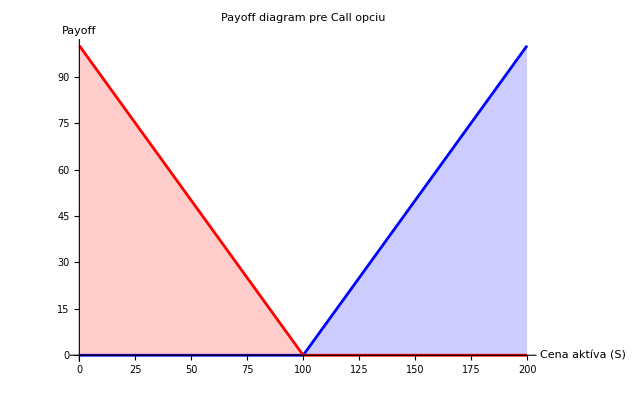

```mathematica
(*2.1*)
K=100; (*Expiračná cena*)
Smax=200; 

callPayoff[S_]:=Max[0,S-K]
putPayoff[S_]:=Max[0,K-S]

(*Vytvorenie dát pre grafy*)
S=Range[0,Smax,1];
callValues=callPayoff/@S;
putValues=putPayoff/@S;

Show[Plot[callPayoff[S],{S,0,Smax},PlotRange->All,AxesLabel->{"Cena aktíva (S)","Payoff"},PlotLabel->"Payoff diagram pre Call opciu",Filling->Axis,PlotStyle->Blue],
Plot[putPayoff[S],{S,0,Smax},PlotRange->All,AxesLabel->{"Cena aktíva (S)","Payoff"},PlotLabel->"Payoff diagram pre Put opciu",Filling->Axis,PlotStyle->Red]]
```

```mathematica
(*2.2*)
```

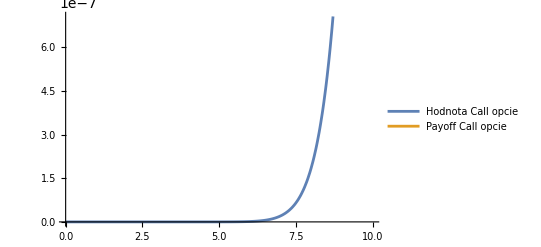

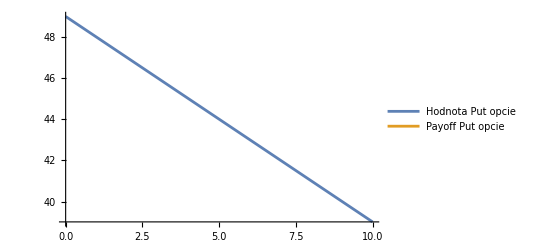

```mathematica
s=Smax;      (*aktuálna cena podkladového aktíva*)
e=K;     (*expiračná cena*)
Sigma=0.5; (*volatilita*)
r=0.04;    (*spojitá úroková miera*)
tau=0.5;   (*čas do expirácie*)
d=0;       (*dividenda*)
(*Funkcie pre d1 a d2*)
d1[S_]:=(Log[S/e]+(r-d+(Sigma^2)/2)*tau)/(Sigma*Sqrt[tau]);
d2[S_]:=d1[S]-Sigma*Sqrt[tau];
(*Funkcie pre hodnotu call a put opcie*)
CallValue[S_]:=S*Exp[-d*tau]*CDF[NormalDistribution[],d1[S]]-e*Exp[-r*tau]*CDF[NormalDistribution[],d2[S]]//N;
PutValue[S_]:=e*Exp[-r*tau]*CDF[NormalDistribution[],-d2[S]]-S*Exp[-d*tau]*CDF[NormalDistribution[],-d1[S]]//N;
Plot[{CallValue[t],callPayoff[t]},{t,0,Smax}, PlotLegends->{"Hodnota Call opcie","Payoff Call opcie"}]
Plot[{PutValue[t],putPayoff[t]},{t,0,Smax}, PlotLegends->{"Hodnota Put opcie","Payoff Put opcie"}]
```

```mathematica
(*2.3*)
```

```mathematica
K=50;          (*Expiračná cena*)
r=0.04;         (*Spojitá úroková miera*)
sigma=0.2;      (*Volatilita*)
Smax=100;       (*Maximálna cena akcie*)
T=1;            (*Exspiračný čas*)
```

```mathematica
blackScholesEq=D[V[t,S],t]+(1/2) sigma^2 S^2 D[V[t,S],{S,2}]+r S D[V[t,S],S]-r V[t,S]==0
callBoundaryConditions={V[T,S]==Max[S-K,0],V[t,0]==0,V[t,Smax]==Max[Smax-K e^{-r (tau)},0]}
callSolution=NDSolve[{blackScholesEq,callBoundaryConditions},V,{t,0,T},{S,0,Smax}]
Plot3D[Evaluate[V[t,S]/. callSolution],{t,0,T},{S,0,Smax},AxesLabel->{"Time (t)","Stock Price (S)","Option Price (V)"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"Black-Scholes Call Option Price"]
```

-0.04 V[t,S]+0.04 S V^(0,1)[t,S]+0.02 S^2 V^(0,2)[t,S]+V^(1,0)[t,S]==0

{V[1,S]==Max[0,-50+S],V[t,0]==0,V[t,100]==53.7629}

-Graphics3D-

```mathematica
ClearAll[V]
```

```mathematica
putBoundaryConditions={V[T,S]==Max[K-S,0],V[t,0]==K Exp[-r (T-t)],V[t,Smax]==Max[K e^{-r (T-t)}-Smax,0]};
putSolution=NDSolve[{blackScholesEq,putBoundaryConditions},V,{t,0,T},{S,0,Smax}];
Plot3D[Evaluate[V[t,S]/. putSolution],{t,0,T},{S,0,Smax},AxesLabel->{"Time (t)","Stock Price (S)","Option Price (V)"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"Black-Scholes Put Option Price"]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable S.

-Graphics3D-